## Setup (run)

```mathematica
$HistoryLength=0;
```

### Load and process data

```mathematica
importReal64MultiList[dir_,template_]:=Module[{filenameTemplate,depth,dimensions,imported},
filenameTemplate=StringTemplate[template];
depth=StringCount[template,"``"];
dimensions=(Length[FileNames[#,dir,1]]&)@*(TemplateApply[filenameTemplate,Table[If[i==#,"*",0],{i,depth}]]&)/@Range[depth];
imported=Array[Import[dir<>filenameTemplate[##],"Real64"]&,dimensions,ConstantArray[0,depth]];
{dimensions,imported}
];
```

```mathematica
importComplex64MultiList[dir_,template_]:=Module[{filenameTemplate,depth,dimensions,imported},
filenameTemplate=StringTemplate[template];
depth=StringCount[template,"``"];
dimensions=(Length[FileNames[#,dir,1]]&)@*(TemplateApply[filenameTemplate,Table[If[i==#,"*",0],{i,depth}]]&)/@Range[depth];
imported=Array[Import[dir<>filenameTemplate[##],"Complex128"]&,dimensions,ConstantArray[0,depth]];
{dimensions,imported}
];
```

```mathematica
importSetup[paramNames_,paramTypes_,dir_,setupFilename_]:=AssociationThread[paramNames->Import[dir<>setupFilename,"Binary","DataFormat"->paramTypes][[1]]];
```

```mathematica
importSetupWithOffset[paramNames_,paramTypes_,paramOffsets_,dir_,setupFilename_]:=Module[{byteArray,paramVal},
byteArray=ByteArray[Import[dir<>"param.dat","Binary"]];
paramVal=Table[ImportByteArray[byteArray[[paramOffsets[[i]]+1;;If[i<Length[paramTypes],paramOffsets[[i+1]],-1]]],paramTypes[[i]]]//(If[Length[#]==1,#[[1]],#]&),{i,Length[paramTypes]}];
AssociationThread[paramNames->paramVal]];
```

```mathematica
readSetup[template_,subparam__]:=Module[{dir,paramNames,paramTypes,paramOffsets,param},
dir=maindir<>(template[subparam]);
paramNames=Import[dir<>"paramNames.txt","List"];
paramTypes=Import[dir<>"paramTypes.txt","List"];
paramOffsets=Import[dir<>"paramOffsets.txt","List"];
param=If[FailureQ[paramOffsets],importSetup[paramNames,paramTypes,dir,"param.dat"],importSetupWithOffset[paramNames,paramTypes,paramOffsets,dir,"param.dat"]];
param
];
```

```mathematica
readSetup[dir_]:=Module[{paramNames,paramTypes,paramOffsets,param},
paramNames=Import[dir<>"paramNames.txt","List"];
paramTypes=Import[dir<>"paramTypes.txt","List"];
paramOffsets=Import[dir<>"paramOffsets.txt","List"];
param=If[FailureQ[paramOffsets],importSetup[paramNames,paramTypes,dir,"param.dat"],importSetupWithOffset[paramNames,paramTypes,paramOffsets,dir,"param.dat"]];
param
];
```

```mathematica
findPowerLaw[ψ_,t1_,t2_]:=(Log[ψ[t2]//Abs]-Log[ψ[t1]//Abs])/(Log[t2]-Log[t1]);
```

### Style setup

```mathematica
LMR="Latin Modern Roman";
Av="Avenir";
Ar="Arial";
TNR="Times New Roman";
BOS="Bookman Old Style";
fontfam=LMR;
nmbrsize=14;
labelsize=12;
episize=12;
framethick=0.003;
thick=0.005;
fs=Directive[{Black,FontFamily->fontfam,FontSize->nmbrsize,Thickness[framethick]}];
```

```mathematica
(*labeledTicks=Table[{10^i,Superscript[10,i]},{i,-16,10,2}];
unlabeledTicks=Flatten[Table[{k*j,Null},{k,2,9},{j,Table[{10^i,Superscript[10,i]},{i,-16,10}][[All,1]]}],1];
evenTicks=Join[labeledTicks,unlabeledTicks];*)
```

```mathematica
labeledTicks=Table[{10^i,Superscript[10,i]},{i,-30,10,1}];
unlabeledTicks=Table[{10^i,Null},{i,-30,10,2}];
```

```mathematica
setFont[text_]:=Style[text,20];
```

### General import script

```mathematica
importRun[maindir_]:=Module[{setup,n,t,nSnapshot,RSnapshot,RhosSnapshot,RhobSnapshot,RhodSnapshot,UsSnapshot,UbSnapshot,UdSnapshot,fracRadii,tRadii,sRadii,bRadii,dRadii},
setup=readSetup[maindir];
n=setup["N"];

t=importReal64MultiList[maindir,"t.dat"][[2]];
nSnapshot=Length[t];

RSnapshot=importReal64MultiList[maindir,"R.dat"][[2]]//Partition[#,n]&;
RhosSnapshot=importReal64MultiList[maindir,"Rho_s.dat"][[2]]//Partition[#,n]&;
RhobSnapshot=importReal64MultiList[maindir,"Rho_b.dat"][[2]]//Partition[#,n]&;
RhodSnapshot=importReal64MultiList[maindir,"Rho_d.dat"][[2]]//Partition[#,n]&;
UsSnapshot=importReal64MultiList[maindir,"U_s.dat"][[2]]//Partition[#,n]&;
UbSnapshot=importReal64MultiList[maindir,"U_b.dat"][[2]]//Partition[#,n]&;
UdSnapshot=importReal64MultiList[maindir,"U_d.dat"][[2]]//Partition[#,n]&;

fracRadii=importReal64MultiList[maindir,"radii_fraction.dat"][[2]];
tRadii=importReal64MultiList[maindir,"radii_t.dat"][[2]];
sRadii=importReal64MultiList[maindir,"radii_s.dat"][[2]]//Partition[#,Length[fracRadii]]&//Transpose;
bRadii=importReal64MultiList[maindir,"radii_b.dat"][[2]]//Partition[#,Length[fracRadii]]&//Transpose;
dRadii=importReal64MultiList[maindir,"radii_d.dat"][[2]]//Partition[#,Length[fracRadii]]&//Transpose;

AssociationThread[{"setup","n","t","nSnapshot","RSnapshot","RhosSnapshot","RhobSnapshot","RhodSnapshot","UsSnapshot","UbSnapshot","UdSnapshot","fracRadii","tRadii","sRadii","bRadii","dRadii"},{setup,n,t,nSnapshot,RSnapshot,RhosSnapshot,RhobSnapshot,RhodSnapshot,UsSnapshot,UbSnapshot,UdSnapshot,fracRadii,tRadii,sRadii,bRadii,dRadii}]
];
```

## One fluid split in two

#### Load data

```mathematica
maindir="output/one_fluid_Yiming/";
setup=readSetup[maindir];
n=setup["N"];

t=importReal64MultiList[maindir,"t.dat"][[2]];
nSnapshot=Length[t];

RSnapshot=importReal64MultiList[maindir,"R.dat"][[2]]//Partition[#,n]&;
RhosSnapshot=importReal64MultiList[maindir,"Rho_s.dat"][[2]]//Partition[#,n]&;
RhobSnapshot=importReal64MultiList[maindir,"Rho_b.dat"][[2]]//Partition[#,n]&;
RhodSnapshot=importReal64MultiList[maindir,"Rho_d.dat"][[2]]//Partition[#,n]&;
UsSnapshot=importReal64MultiList[maindir,"U_s.dat"][[2]]//Partition[#,n]&;
UbSnapshot=importReal64MultiList[maindir,"U_b.dat"][[2]]//Partition[#,n]&;
UdSnapshot=importReal64MultiList[maindir,"U_d.dat"][[2]]//Partition[#,n]&;

fracRadii=importReal64MultiList[maindir,"radii_fraction.dat"][[2]];
tRadii=importReal64MultiList[maindir,"radii_t.dat"][[2]];
sRadii=importReal64MultiList[maindir,"radii_s.dat"][[2]]//Partition[#,Length[fracRadii]]&//Transpose;
bRadii=importReal64MultiList[maindir,"radii_b.dat"][[2]]//Partition[#,Length[fracRadii]]&//Transpose;
dRadii=importReal64MultiList[maindir,"radii_d.dat"][[2]]//Partition[#,Length[fracRadii]]&//Transpose;

RSnapshot1=RSnapshot;
RhosSnapshot1=RhosSnapshot;
UsSnapshot1=UsSnapshot;

fracRadii1=fracRadii;
tRadii1=tRadii;
sRadii1=sRadii;
bRadii1=bRadii;
dRadii1=dRadii;
```

```mathematica
maindir="output/one_fluid_split_in_two_Yiming/";
setup=readSetup[maindir];
n=setup["N"];

t=importReal64MultiList[maindir,"t.dat"][[2]];
nSnapshot=Length[t];

RSnapshot=importReal64MultiList[maindir,"R.dat"][[2]]//Partition[#,n]&;
RhosSnapshot=importReal64MultiList[maindir,"Rho_s.dat"][[2]]//Partition[#,n]&;
RhobSnapshot=importReal64MultiList[maindir,"Rho_b.dat"][[2]]//Partition[#,n]&;
RhodSnapshot=importReal64MultiList[maindir,"Rho_d.dat"][[2]]//Partition[#,n]&;
UsSnapshot=importReal64MultiList[maindir,"U_s.dat"][[2]]//Partition[#,n]&;
UbSnapshot=importReal64MultiList[maindir,"U_b.dat"][[2]]//Partition[#,n]&;
UdSnapshot=importReal64MultiList[maindir,"U_d.dat"][[2]]//Partition[#,n]&;

fracRadii=importReal64MultiList[maindir,"radii_fraction.dat"][[2]];
tRadii=importReal64MultiList[maindir,"radii_t.dat"][[2]];
sRadii=importReal64MultiList[maindir,"radii_s.dat"][[2]]//Partition[#,Length[fracRadii]]&//Transpose;
bRadii=importReal64MultiList[maindir,"radii_b.dat"][[2]]//Partition[#,Length[fracRadii]]&//Transpose;
dRadii=importReal64MultiList[maindir,"radii_d.dat"][[2]]//Partition[#,Length[fracRadii]]&//Transpose;
```

#### ρ plot

```mathematica
rhoToPlot={
Table[{RSnapshot[[i]],RhosSnapshot[[i]]}ᵀ,{i,nSnapshot}],
Table[{RSnapshot[[i]],RhodSnapshot[[i]]}ᵀ,{i,nSnapshot}],
Table[{RSnapshot[[i]],RhosSnapshot[[i]]+RhodSnapshot[[i]]}ᵀ,{i,nSnapshot}],
Table[{RSnapshot1[[i]],RhosSnapshot1[[i]]}ᵀ,{i,nSnapshot}]
}//Transpose//Flatten[#,1]&;
```

```mathematica
legends=Table[StringTemplate["`` t̂=``"]@@config,{config,Table[{
{"star",DecimalForm[t[[i]],{10,4}]},
{"DM",DecimalForm[t[[i]],{10,4}]},
{"total",DecimalForm[t[[i]],{10,4}]},
{"one-fluid",DecimalForm[t[[i]],{10,4}]}
},{i,nSnapshot}]//Flatten[#,1]&}];
```

```mathematica
(*style=Table[{{color,setting}},{color,{Darker[Red],Darker[Green],Black,Blue}},{setting,{Dashed,Thickness[0.002],DotDashed}}]//Flatten[#,2]&;*)
```

```mathematica
style={{Darker[Red],Dashed},{Darker[Green],DotDashed},{Gray},{Darker[Blue],Dashed}};
```

```mathematica
plot=ListLogLogPlot[rhoToPlot,Joined->True,
PlotRange->{{10^-6,10^2},{10^-10,10^10}},
PlotLegends->Placed[LineLegend[legends,LabelStyle->{FontFamily->fontfam,FontSize->15}],{Right,Top}],
PlotStyle->style,
Frame->True,
FrameStyle->Directive[{Black,FontFamily->fontfam,FontSize->18,Thickness[framethick]}],
FrameLabel->{{"ρ̂",None},{"r̂","One-fluid-split-in-two (ξ,ζ)=(1,1)"}},
FrameTicks->{{labeledTicks,None},{labeledTicks,None}},
ImageSize->800,
AspectRatio->1
(*Epilog->{Text[Style["(ξ,ζ)=(1,1)",24,FontFamily->fontfam],Scaled[{0.1,0.1}]]}*)
]
```

```mathematica
filename="split_in_two_comparison_rho.pdf";
Export[NotebookDirectory[]<>filename,plot];
```

#### σ plot

```mathematica
σToPlot={
Table[{RSnapshot[[i]],√(2/3 UsSnapshot[[i]])}ᵀ,{i,nSnapshot}],
Table[{RSnapshot[[i]],√(2/3 UdSnapshot[[i]])}ᵀ,{i,nSnapshot}],
Table[{RSnapshot1[[i]],√(2/3 UsSnapshot1[[i]])}ᵀ,{i,nSnapshot}]
}//Transpose//Flatten[#,1]&;
```

```mathematica
legends=Table[StringTemplate["`` t̂=``"]@@config,{config,Table[{
{"star",DecimalForm[t[[i]],{10,4}]},
{"DM",DecimalForm[t[[i]],{10,4}]},
{"one-fluid",DecimalForm[t[[i]],{10,4}]}
},{i,nSnapshot}]//Flatten[#,1]&}]
```

{star t̂=0.0000,DM t̂=0.0000,one-fluid t̂=0.0000,star t̂=5.5001,DM t̂=5.5001,one-fluid t̂=5.5001,star t̂=5.5650,DM t̂=5.5650,one-fluid t̂=5.5650,star t̂=5.5652,DM t̂=5.5652,one-fluid t̂=5.5652}

```mathematica
style={{Darker[Red],Dashed},{Darker[Green],DotDashed},{Darker[Blue],Dashed}};
```

```mathematica
plot=ListLogLogPlot[σToPlot,Joined->True,
PlotRange->{{10^-6,10^2},{0.2,0.8}},
PlotLegends->Placed[LineLegend[legends,LabelStyle->{FontFamily->fontfam,FontSize->15}],{Right,Top}],
PlotStyle->style,
Frame->True,
FrameStyle->Directive[{Black,FontFamily->fontfam,FontSize->18,Thickness[framethick]}],
FrameLabel->{{"σ̂",None},{"r̂","One-fluid-split-in-two (ξ,ζ)=(1,1)"}},
(*FrameTicks->{{labeledTicks,None},{Automatic,None}},*)
ImageSize->800,
AspectRatio->1
(*Epilog->{Text[Style["One Fluid",24,FontFamily->fontfam],Scaled[{0.5,0.1}]]}*)
]
```

```mathematica
filename="split_in_two_comparison_sigma.pdf";
Export[NotebookDirectory[]<>filename,plot];
```

#### Radii plot

```mathematica
radiusToPlot=Table[{tRadii1,sRadii1[[i]]}ᵀ,{i,Length[fracRadii]}];

legends=Table[StringTemplate["M(r)/M(∞) = ``"]@config,{config,fracRadii}];
style=Table[{Red},{Length[fracRadii]}]~Join~Table[{Blue},{Length[fracRadii]}];
```

```mathematica
ListLogPlot[radiusToPlot,
Joined->True,
PlotRange->{Full,{0.1,4}},
PlotStyle->style,
Frame->True,
FrameStyle->Directive[{Black,FontFamily->fontfam,FontSize->18,Thickness[framethick]}],
FrameLabel->{{"r̂",None},{"t̂","Lagrangian Radii (One-fluid)"}},
PlotLegends->Placed[LineLegend[legends~Join~legends,LabelStyle->{FontFamily->fontfam,FontSize->15}],{Right,Top}],
ImageSize->600
]
```

```mathematica
filename="one_fluid_radii.pdf";
Export[NotebookDirectory[]<>filename,plot];
```

## Tidal effect comparison (single)

```mathematica
withoutTidalData=importRun["output/one_fluid_without_tidal/"];
withTidalData=importRun["output/one_fluid_with_tidal/"];
```

```mathematica
nSnapshot=withoutTidalData["nSnapshot"];
RSnapshot=withTidalData["RSnapshot"];
RhosSnapshot=withTidalData["RhosSnapshot"];
UsSnapshot=withTidalData["UsSnapshot"];
RSnapshot1=withoutTidalData["RSnapshot"];
RhosSnapshot1=withoutTidalData["RhosSnapshot"];
UsSnapshot1=withoutTidalData["UsSnapshot"];
t=withoutTidalData["t"];
```

#### ρ plot

```mathematica
rhoToPlot={
Table[{RSnapshot[[i]],RhosSnapshot[[i]]}ᵀ,{i,nSnapshot}],
Table[{RSnapshot1[[i]],RhosSnapshot1[[i]]}ᵀ,{i,nSnapshot}]
}//Transpose//Flatten[#,1]&;
```

```mathematica
legends=Table[StringTemplate["`` t̂=``"]@@config,{config,Table[{
{"with tidal",DecimalForm[t[[i]],{10,4}]},
{"without tidal",DecimalForm[t[[i]],{10,4}]}
},{i,nSnapshot}]//Flatten[#,1]&}];
```

```mathematica
style={{Darker[Red],Thickness[0.002]},{Darker[Green],Dashed}};
```

```mathematica
plot=ListLogLogPlot[rhoToPlot,Joined->True,
PlotRange->{{10^-5,10^4},{10^-10,10^7}},
PlotLegends->Placed[LineLegend[legends,LabelStyle->{FontFamily->fontfam,FontSize->15}],{Right,Top}],
PlotStyle->style,
Frame->True,
FrameStyle->Directive[{Black,FontFamily->fontfam,FontSize->18,Thickness[framethick]}],
FrameLabel->{{"ρ̂",None},{"r̂","Tidal effect (one fluid, cutoff = 10^1)"}},
FrameTicks->{{labeledTicks,None},{labeledTicks,None}},
ImageSize->600,
AspectRatio->1
(*Epilog->{Text[Style["(ξ,ζ)=(1,1)",24,FontFamily->fontfam],Scaled[{0.1,0.1}]]}*)
]
```

```mathematica
filename="tidal_effect_one_fluid_comparison_rho.pdf";
Export[NotebookDirectory[]<>filename,plot];
```

#### σ plot

```mathematica
σToPlot={
Table[{RSnapshot[[i]],√(2/3 UsSnapshot[[i]])}ᵀ,{i,nSnapshot}],
Table[{RSnapshot1[[i]],√(2/3 UsSnapshot1[[i]])}ᵀ,{i,nSnapshot}]
}//Transpose//Flatten[#,1]&;
```

```mathematica
plot=ListLogLogPlot[σToPlot,Joined->True,
PlotRange->{{10^-5,10^4},{0.05,0.8}},
PlotLegends->Placed[LineLegend[legends,LabelStyle->{FontFamily->fontfam,FontSize->15}],{Right,Top}],
PlotStyle->style,
Frame->True,
FrameStyle->Directive[{Black,FontFamily->fontfam,FontSize->18,Thickness[framethick]}],
FrameLabel->{{"σ̂",None},{"r̂","Tidal effect (one fluid, cutoff = 10^1)"}},
(*FrameTicks->{{labeledTicks,None},{Automatic,None}},*)
ImageSize->600,
AspectRatio->1
(*Epilog->{Text[Style["One Fluid",24,FontFamily->fontfam],Scaled[{0.5,0.1}]]}*)
]
```

```mathematica
filename="tidal_effect_one_fluid_comparison_sigma.pdf";
Export[NotebookDirectory[]<>filename,plot];
```

#### Radii plot

```mathematica
tRadii1=withoutTidalData["tRadii"];
sRadii1=withoutTidalData["sRadii"];
tRadii=withTidalData["tRadii"];
sRadii=withTidalData["sRadii"];
fracRadii=withoutTidalData["fracRadii"];
```

```mathematica
radiusToPlot=Table[{tRadii1,sRadii1[[i]]}ᵀ,{i,Length[fracRadii]}]~Join~Table[{tRadii,sRadii[[i]]}ᵀ,{i,Length[fracRadii]}];

legends=Table[StringTemplate["no-tidal (``)"]@config,{config,fracRadii}]~Join~Table[StringTemplate["tidal (``)"]@config,{config,fracRadii}];
style=Table[{Red},{Length[fracRadii]}]~Join~Table[{Blue},{Length[fracRadii]}];
```

```mathematica
plot=ListLogPlot[radiusToPlot,
Joined->True,
PlotRange->{Full,{0.1,4}},
PlotStyle->style,
Frame->True,
FrameStyle->Directive[{Black,FontFamily->fontfam,FontSize->18,Thickness[framethick]}],
FrameLabel->{{"r̂",None},{"t̂","Lagrangian Radii (One-fluid)"}},
PlotLegends->Placed[LineLegend[legends~Join~legends,LabelStyle->{FontFamily->fontfam,FontSize->15}],{Right,Top}],
ImageSize->600
]
```

```mathematica
filename="one_fluid_radii.pdf";
Export[NotebookDirectory[]<>filename,plot];
```

## Comparison with AB

```mathematica
withoutTidalData=importRun["output/baseline_AB/"];
withTidalData=importRun["output/with_tidal_AB/"];
```

```mathematica
nSnapshot=withoutTidalData["nSnapshot"];
t=withoutTidalData["t"];
```

```mathematica
RSnapshot=withTidalData["RSnapshot"];
RhosSnapshot=withTidalData["RhosSnapshot"];
RhodSnapshot=withTidalData["RhodSnapshot"];
UsSnapshot=withTidalData["UsSnapshot"];
UdSnapshot=withTidalData["UdSnapshot"];
RSnapshot1=withoutTidalData["RSnapshot"];
RhosSnapshot1=withoutTidalData["RhosSnapshot"];
RhodSnapshot1=withoutTidalData["RhodSnapshot"];
UsSnapshot1=withoutTidalData["UsSnapshot"];
UdSnapshot1=withoutTidalData["UdSnapshot"];
```

```mathematica
tRadii1=withoutTidalData["tRadii"];
sRadii1=withoutTidalData["sRadii"];
dRadii1=withoutTidalData["dRadii"];
tRadii=withTidalData["tRadii"];
sRadii=withTidalData["sRadii"];
dRadii=withTidalData["dRadii"];
fracRadii=withoutTidalData["fracRadii"];
```

#### ρ plot (without tidal)

```mathematica
rhoToPlot={
Table[{RSnapshot1[[i]],RhosSnapshot1[[i]]}ᵀ,{i,nSnapshot}],
Table[{RSnapshot1[[i]],RhodSnapshot1[[i]]}ᵀ,{i,nSnapshot}]
}//Transpose//Flatten[#,1]&;
```

```mathematica
legends=Table[StringTemplate["`` t̂=``"]@@config,{config,Table[{
{"single",DecimalForm[t[[i]],{10,4}]},
{"DM",DecimalForm[t[[i]],{10,4}]}
},{i,nSnapshot}]//Flatten[#,1]&}];
```

```mathematica
style={{Darker[Red],Thickness[0.002]},{Darker[Green],Dashed}};
```

```mathematica
colors=ColorData["Rainbow"]/@Subdivide[0,1,Length[rhoToPlot]/2-1];
style=Table[{c,s},{c,colors},{s,{Thickness[0.003],Dashed}}]//Flatten[#,1]&
```

{{RGBColor[0.471412, 0.108766, 0.527016],Thickness[0.003]},{RGBColor[0.471412, 0.108766, 0.527016],Dashing[{Small,Small}]},{RGBColor[0.266122, 0.486664, 0.802529],Thickness[0.003]},{RGBColor[0.266122, 0.486664, 0.802529],Dashing[{Small,Small}]},{RGBColor[0.513417, 0.72992, 0.440682],Thickness[0.003]},{RGBColor[0.513417, 0.72992, 0.440682],Dashing[{Small,Small}]},{RGBColor[0.863512, 0.670771, 0.236564],Thickness[0.003]},{RGBColor[0.863512, 0.670771, 0.236564],Dashing[{Small,Small}]},{RGBColor[0.857359, 0.131106, 0.132128],Thickness[0.003]},{RGBColor[0.857359, 0.131106, 0.132128],Dashing[{Small,Small}]}}

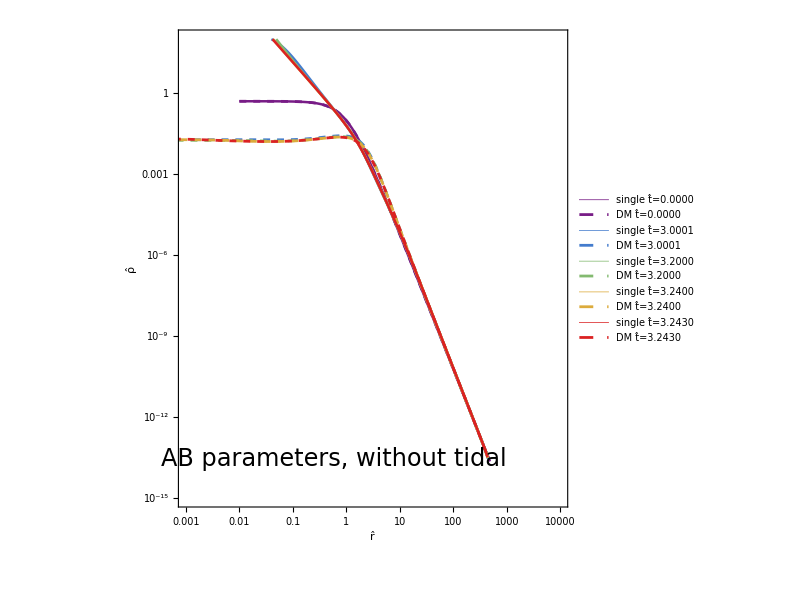

```mathematica
plot=ListLogLogPlot[rhoToPlot,Joined->True,
PlotRange->{{10^-3,10^4},{10^-15,10^2}},
PlotLegends->Placed[LineLegend[legends,LabelStyle->{FontFamily->fontfam,FontSize->15}],{Right,Top}],
PlotLabels->Placed[Automatic,Above],
PlotStyle->style,
Frame->True,
FrameStyle->Directive[{Black,FontFamily->fontfam,FontSize->18,Thickness[framethick]}],
FrameLabel->{{"ρ̂",None},{"r̂",""}},
FrameTicks->{{labeledTicks,None},{labeledTicks,None}},
ImageSize->600,
AspectRatio->1,
Epilog->{Text[Style["AB parameters, without tidal",24,FontFamily->fontfam],Scaled[{0.4,0.1}]]}
]
```

```mathematica
filename="AB_rho_without_tidal.pdf";
Export[NotebookDirectory[]<>filename,plot];
```

#### σ plot (without tidal)

```mathematica
σToPlot={
Table[{RSnapshot1[[i]],√(2/3 UsSnapshot1[[i]])}ᵀ,{i,nSnapshot}],
Table[{RSnapshot1[[i]],√(2/3 UdSnapshot1[[i]])}ᵀ,{i,nSnapshot}]
}//Transpose(*//#[[{1,2}]]&*)//Flatten[#,1]&;
```

```mathematica
plot=ListLogLogPlot[σToPlot,Joined->True,
PlotRange->{{10^-5,10^4},{0.05,2}},
PlotLegends->Placed[LineLegend[legends,LabelStyle->{FontFamily->fontfam,FontSize->15}],{Right,Top}],
PlotStyle->style,
Frame->True,
FrameStyle->Directive[{Black,FontFamily->fontfam,FontSize->18,Thickness[framethick]}],
FrameLabel->{{"σ̂",None},{"r̂",""}},
(*FrameTicks->{{labeledTicks,None},{Automatic,None}},*)
ImageSize->600,
AspectRatio->1,
Epilog->{Text[Style["AB parameters, without tidal",24,FontFamily->fontfam],Scaled[{0.4,0.1}]]}
]
```

```mathematica
filename="AB_sigma_without_tidal.pdf";
Export[NotebookDirectory[]<>filename,plot];
```

#### Radius plot (without tidal)

```mathematica
legends=Table[StringTemplate["M(r)/M(∞) = ``"]@config,{config,fracRadii}]
```

{M(r)/M(∞) = 0.01,M(r)/M(∞) = 0.05,M(r)/M(∞) = 0.1,M(r)/M(∞) = 0.2,M(r)/M(∞) = 0.5,M(r)/M(∞) = 0.7}

```mathematica
(*radiusToPlot=Table[{tRadii1,dRadii1[[i]]}ᵀ,{i,Length[fracRadii]}]~Join~Table[{tRadii,dRadii[[i]]}ᵀ,{i,Length[fracRadii]}];

legends=Table[StringTemplate["no-tidal (``)"]@config,{config,fracRadii}]~Join~Table[StringTemplate["tidal (``)"]@config,{config,fracRadii}];
style=Table[{Red},{Length[fracRadii]}]~Join~Table[{Blue},{Length[fracRadii]}];*)
```

```mathematica
radiusToPlot=Table[{tRadii1,sRadii1[[i]]}ᵀ,{i,Length[fracRadii]}]~Join~Table[{tRadii1,dRadii1[[i]]}ᵀ,{i,Length[fracRadii]}];

legends=Table[StringTemplate["Star (``)"]@config,{config,fracRadii}]~Join~Table[StringTemplate["DM (``)"]@config,{config,fracRadii}];
style=Table[{Red},{Length[fracRadii]}]~Join~Table[{Blue},{Length[fracRadii]}];
```

```mathematica
plot=ListLogPlot[radiusToPlot,
Joined->True,
PlotRange->{Full,{0.1,4}},
PlotStyle->style,
Frame->True,
FrameStyle->Directive[{Black,FontFamily->fontfam,FontSize->18,Thickness[framethick]}],
FrameLabel->{{"r̂",None},{"t̂","Lagrangian Radii (AB, no-tidal)"}},
PlotLegends->Placed[LineLegend[legends~Join~legends,LabelStyle->{FontFamily->fontfam,FontSize->15}],After(*{Right,Top}*)],
ImageSize->600
]
```

```mathematica
filename="AB_radii_without_tidal.pdf";
Export[NotebookDirectory[]<>filename,plot];
```

#### Radius plot (with tidal)

```mathematica
legends=Table[StringTemplate["M(r)/M(∞) = ``"]@config,{config,fracRadii}]
```

{M(r)/M(∞) = 0.01,M(r)/M(∞) = 0.05,M(r)/M(∞) = 0.1,M(r)/M(∞) = 0.2,M(r)/M(∞) = 0.5,M(r)/M(∞) = 0.7}

```mathematica
radiusToPlot=Table[{tRadii,sRadii[[i]]}ᵀ,{i,Length[fracRadii]}]~Join~Table[{tRadii,dRadii[[i]]}ᵀ,{i,Length[fracRadii]}];

legends=Table[StringTemplate["Star (``)"]@config,{config,fracRadii}]~Join~Table[StringTemplate["DM (``)"]@config,{config,fracRadii}];
style=Table[{Red},{Length[fracRadii]}]~Join~Table[{Blue},{Length[fracRadii]}];
```

```mathematica
plot=ListLogPlot[radiusToPlot,
Joined->True,
PlotRange->{Full,{0.1,4}},
PlotStyle->style,
Frame->True,
FrameStyle->Directive[{Black,FontFamily->fontfam,FontSize->18,Thickness[framethick]}],
FrameLabel->{{"r̂",None},{"t̂","Lagrangian Radii (AB, with-tidal)"}},
PlotLegends->Placed[LineLegend[legends~Join~legends,LabelStyle->{FontFamily->fontfam,FontSize->15}],After],
ImageSize->600,
Epilog->{Text[Style[StringTemplate["Tidal radius = ``, k = ``"]@@Values[withTidalData["setup"][[{"tidal_radius","tidal_cutoff_factor"}]]],24,FontFamily->fontfam],Scaled[{0.4,0.9}]]}
]
```

```mathematica
filename="AB_radii_with_tidal.pdf";
Export[NotebookDirectory[]<>filename,plot];
```

```mathematica
withTidalData["setup"][[{"tidal_radius","tidal_cutoff_factor"}]]
Values[withTidalData["setup"][[{"tidal_radius","tidal_cutoff_factor"}]]]
```

<|tidal_radius→2.,tidal_cutoff_factor→10.|>